## singlet

```mathematica
pTratesin=({{0.10003553909920117, 1000, 12.779048656409731, 0.0003147435532216307}, {0.10003562088404373, 1200, 777.3977992521307, 0.2123252585546312}, {0.10003553909920117, 1500, 53324.48028818497, 147.08157100890534}, {0.10003545731435862, 1800, 663610.6060214065, 7893.348590518401}, {0.1000356754072721, 2000, 1.7148222856785036*^6, 40962.1278116474}, {10.003553909920118, 1000, 12.688990367415565, 0.00030694241439896186}, {10.003562088404372, 1200, 777.3794325758431, 0.21227835995845165}, {10.003553909920118, 1500, 54686.40672731331, 150.83693246431307}, {10.003545731435862, 1800, 1.0279349964204162*^6, 12224.721361011325}, {10.003567540727209, 2000, 4.388461123055906*^6, 104669.15259037481}, {1.0003553909920118, 1000, 12.778801920718555, 0.00031462585635400324}, {1.0003562088404372, 1200, 777.507787641154, 0.2123546991562696}, {1.0003553909920118, 1500, 54546.35445119008, 150.45170251008628}, {1.0003545731435861, 1800, 944219.5354317126, 11229.18725710173}, {1.0003567540727212, 2000, 3.2115507804171555*^6, 76612.1363357225}})
```

{{0.100036,1000,12.779,0.000314744},{0.100036,1200,777.398,0.212325},{0.100036,1500,53324.5,147.082},{0.100035,1800,663611.,7893.35},{0.100036,2000,1.71482×10^6,40962.1},{10.0036,1000,12.689,0.000306942},{10.0036,1200,777.379,0.212278},{10.0036,1500,54686.4,150.837},{10.0035,1800,1.02793×10^6,12224.7},{10.0036,2000,4.38846×10^6,104669.},{1.00036,1000,12.7788,0.000314626},{1.00036,1200,777.508,0.212355},{1.00036,1500,54546.4,150.452},{1.00035,1800,944220.,11229.2},{1.00036,2000,3.21155×10^6,76612.1}}

```mathematica
(*tell how many pressure*)
pListsin={};
For[i=1,i≤ Length[pTratesin],i++,
If[MemberQ[pListsin,Round[pTratesin⟦i,1⟧*100]/100.0]==False,
AppendTo[pListsin,Round[pTratesin⟦i,1⟧*100]/100.0]
]
];
pListsin
```

{0.1,10.,1.}

```mathematica
(*3-parameter-fitting*)
Tratesin=Table[{},{i,1,Length[pListsin]}]; (* Trate⟦i⟧ stores k(T) at pi *)
pTFitkforsin=Table[{},{i,1,Length[pListsin]}]; 
pTFitkbacsin=Table[{},{i,1,Length[pListsin]}]; 
For[i=1,i≤ Length[pListsin],i++,
For[j=1,j≤ Length[pTratesin],j++,
If [Abs[pTratesin⟦j,1⟧/pListsin⟦i⟧-1]<0.01,AppendTo[Tratesin⟦i⟧,pTratesin⟦j,2;;4⟧]]
];
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]]*)
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkfor2p⟦i,1,2⟧},n,{Ea,pTFitkfor2p⟦i,3,2⟧}},T,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkbac2p⟦i,1,2⟧},n,{Ea,pTFitkbac2p⟦i,3,2⟧}},T,MaxIterations-> 100000]]*)
pTFitkforsin⟦i⟧=Simplify[Exp[Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Tratesin⟦i,All,{1,2}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]]];
pTFitkbacsin⟦i⟧=Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Tratesin⟦i,All,{1,3}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]//Exp//Simplify;
];
Tratesin
pTFitkforsin
pTFitkbacsin
```

{{{1000,12.779,0.000314744},{1200,777.398,0.212325},{1500,53324.5,147.082},{1800,663611.,7893.35},{2000,1.71482×10^6,40962.1}},{{1000,12.689,0.000306942},{1200,777.379,0.212278},{1500,54686.4,150.837},{1800,1.02793×10^6,12224.7},{2000,4.38846×10^6,104669.}},{{1000,12.7788,0.000314626},{1200,777.508,0.212355},{1500,54546.4,150.452},{1800,944220.,11229.2},{2000,3.21155×10^6,76612.1}}}

{(3.3562×10^34 ⅇ^(-32783.4/T))/T^6.40204,1274.2 ⅇ^(-22054./T) T^2.52441,(4.96418×10^13 ⅇ^(-25717.7/T))/T^0.477579}

{(2.23949×10^44 ⅇ^(-49794.3/T))/T^8.75045,3.65862×10^13 ⅇ^(-39334.8/T) T^0.00140031,(3.78938×10^23 ⅇ^(-42750.1/T))/T^2.84241}

```mathematica
CTSTsubsin={k1b->2.0288703185987336*^13 ⅇ^(-3734.443117278098/T) T^0.102159024211284,k1f->3143.874522239371 ⅇ^(-14309.747624641917/T) T^2.710823987334233,k2b->1.1318714935703922*^13 ⅇ^(-1577.2078548080892/T) T^0.06673968116497866,k2f->1.1275869173002361*^13 ⅇ^(-1597.5009119371275/T) T^0.07659783162731554,k3b->4.287458164341173*^11 ⅇ^(-38789.67862738626/T) T^0.5587148065421365,k3f->4.002919428869775*^10 ⅇ^(-10698.04608110448/T) T^0.5662706284771529};
```

```mathematica
HPLkforsin=(k1f k2f k3f)/(k2f k3f+k1b (k2b+k3f))/.CTSTsubsin
```

(1.41903×10^27 ⅇ^(-26605.3/T) T^3.35369)/(2.02887×10^13 ⅇ^(-3734.44/T) (1.13187×10^13 ⅇ^(-1577.21/T) T^0.0667397+4.00292×10^10 ⅇ^(-10698./T) T^0.566271) T^0.102159+4.51364×10^23 ⅇ^(-12295.5/T) T^0.642868)

```mathematica
pIverseTFitkforsin=AppendTo[pTFitkforsin,HPLkforsin]/.(T-> 1000/β);
```

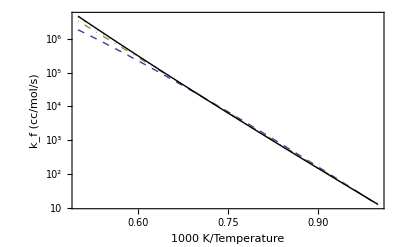

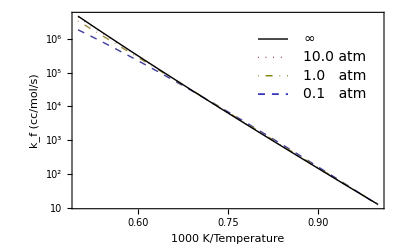

```mathematica
plotframeKeqT={{Style["k_f (cc/mol/s) ",(*Italic,*)14],},{Style["1000 K/Temperature",(*Italic,*)14],}};
leftticks={{10,10,{0.015,0}},{20,,{0.005,0}},{30,,{0.005,0}},{40,,{0.005,0}},{50,,{0.005,0}},{60,,{0.005,0}},{70,,{0.005,0}},{80,,{0.005,0}},{90,,{0.005,0}},{100,DisplayForm[SuperscriptBox[10,2]],{0.015,0}},{200,,{0.005,0}},{300,,{0.005,0}},{400,,{0.005,0}},{500,,{0.005,0}},{600,,{0.005,0}},{700,,{0.005,0}},{800,,{0.005,0}},{900,,{0.005,0}},{1000,DisplayForm[SuperscriptBox[10,3]],{0.015,0}},{2000,,{0.005,0}},{3000,,{0.005,0}},{4000,,{0.005,0}},{5000,,{0.005,0}},{6000,,{0.005,0}},{7000,,{0.005,0}},{8000,,{0.005,0}},{9000,,{0.005,0}},{10000,DisplayForm[SuperscriptBox[10,4]],{0.015,0}},{20000,,{0.005,0}},{30000,,{0.005,0}},{40000,,{0.005,0}},{50000,,{0.005,0}},{60000,,{0.005,0}},{70000,,{0.005,0}},{80000,,{0.005,0}},{90000,,{0.005,0}},{100000,DisplayForm[SuperscriptBox[10,5]],{0.015,0}},{200000,,{0.005,0}},{300000,,{0.005,0}},{400000,,{0.005,0}},{500000,,{0.005,0}},{600000,,{0.005,0}},{700000,,{0.005,0}},{800000,,{0.005,0}},{900000,,{0.005,0}},{1000000,DisplayForm[SuperscriptBox[10,6]],{0.015,0}},{2000000,,{0.005,0}},{3000000,,{0.005,0}},{4000000,,{0.005,0}},{5000000,,{0.005,0}}};
pIverseTFitkforPlotsin=LogPlot[pIverseTFitkforsin,{β,0.5,1},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,FrameTicks-> {{leftticks,Automatic},{Automatic,Automatic }},
                  AxesStyle->Dashed,
                   PlotStyle-> {Dashed,{Thick,Dotted},{Thick,(*Dashing[{0.01,Small}]*)DotDashed},{Thick,Black}}]
(*Blue 0.1 atm. Yellow 1.0 atm. Purple 10.0 atm. Green HPL*)
FMTtext={14(*,Bold*)};
labelstart=0.80;
labelend=0.85;
textposition=0.875;
toplabel=10^6;
deltalabel=3.5;
plotlable=Graphics[{{Darker[Black,.5],Thick,Line[{{labelstart,Log[toplabel]},{labelend,Log[toplabel]}}]},Text[Style["∞",FMTtext],{textposition,Log[toplabel]},{-1,0}],
                                        {Darker[Red,.5],Dotted,Line[{{labelstart,Log[toplabel/deltalabel]},{labelend,Log[toplabel/deltalabel]}}]},Text[Style["10.0 atm",FMTtext],{textposition,Log[toplabel/deltalabel]},{-1,0}],
                                        {Darker[Yellow,.5],Thick,DotDashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel]}}]},Text[Style["1.0   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel]},{-1,0}],
                                        {Darker[Blue],Dashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel/deltalabel]}}]},Text[Style["0.1   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel/deltalabel]},{-1,0}]}];
Show[pIverseTFitkforPlotsin,plotlable]
```

## triplet

```mathematica
pTratetri={{0.10003553909920117,1000,2122.0310021314103,0.034430510012793014},{0.10003562088404373,1200,47962.44432364078,9.434917727488465},{0.10003553909920117,1500,1.0875663717676834*^6,2364.726170123681},{0.10003545731435862,1800,5.018942549962207*^6,50064.70661824387},{0.1000356754072721,2000,1.178711802441688*^7,244024.29685369905},{10.003553909920118,1000,2108.1557722198704,0.03394197149555526},{10.003562088404372,1200,48043.387594435924,9.449669661729626},{10.003553909920118,1500,1.2500265367673635*^6,2717.9098859860496},{10.003545731435862,1800,1.1587765875974514*^7,115439.25025401633},{10.003567540727209,2000,3.1881469602077324*^7,656810.2395653304},{1.0003553909920118,1000,2121.9839122388885,0.03442779229915746},{1.0003562088404372,1200,48041.10165634058,9.450382409343955},{1.0003553909920118,1500,1.227950566298891*^6,2669.9314369123995},{1.0003545731435861,1800,8.942921219688455*^6,89103.04116200787},{1.0003567540727212,2000,1.9613435426413223*^7,404487.11739447707}}
```

{{0.100036,1000,2122.03,0.0344305},{0.100036,1200,47962.4,9.43492},{0.100036,1500,1.08757×10^6,2364.73},{0.100035,1800,5.01894×10^6,50064.7},{0.100036,2000,1.17871×10^7,244024.},{10.0036,1000,2108.16,0.033942},{10.0036,1200,48043.4,9.44967},{10.0036,1500,1.25003×10^6,2717.91},{10.0035,1800,1.15878×10^7,115439.},{10.0036,2000,3.18815×10^7,656810.},{1.00036,1000,2121.98,0.0344278},{1.00036,1200,48041.1,9.45038},{1.00036,1500,1.22795×10^6,2669.93},{1.00035,1800,8.94292×10^6,89103.},{1.00036,2000,1.96134×10^7,404487.}}

```mathematica
(*tell how many pressure*)
pListtri={};
For[i=1,i≤ Length[pTratetri],i++,
If[MemberQ[pListtri,Round[pTratetri⟦i,1⟧*100]/100.0]==False,
AppendTo[pListtri,Round[pTratetri⟦i,1⟧*100]/100.0]
]
];
pListtri
```

{0.1,10.,1.}

```mathematica
(*3-parameter-fitting*)
Tratetri=Table[{},{i,1,Length[pListtri]}]; (* Trate⟦i⟧ stores k(T) at pi *)
pTFitkfortri=Table[{},{i,1,Length[pListtri]}]; 
pTFitkbactri=Table[{},{i,1,Length[pListtri]}]; 
For[i=1,i≤ Length[pListtri],i++,
For[j=1,j≤ Length[pTratetri],j++,
If [Abs[pTratetri⟦j,1⟧/pListtri⟦i⟧-1]<0.01,AppendTo[Tratetri⟦i⟧,pTratetri⟦j,2;;4⟧]]
];
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]]*)
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkfor2p⟦i,1,2⟧},n,{Ea,pTFitkfor2p⟦i,3,2⟧}},T,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkbac2p⟦i,1,2⟧},n,{Ea,pTFitkbac2p⟦i,3,2⟧}},T,MaxIterations-> 100000]]*)
pTFitkfortri⟦i⟧=Simplify[Exp[Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Tratetri⟦i,All,{1,2}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]]];
pTFitkbactri⟦i⟧=Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Tratetri⟦i,All,{1,3}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]//Exp//Simplify;
];
Tratetri
pTFitkfortri
pTFitkbactri
```

{{{1000,2122.03,0.0344305},{1200,47962.4,9.43492},{1500,1.08757×10^6,2364.73},{1800,5.01894×10^6,50064.7},{2000,1.17871×10^7,244024.}},{{1000,2108.16,0.033942},{1200,48043.4,9.44967},{1500,1.25003×10^6,2717.91},{1800,1.15878×10^7,115439.},{2000,3.18815×10^7,656810.}},{{1000,2121.98,0.0344278},{1200,48041.1,9.45038},{1500,1.22795×10^6,2669.93},{1800,8.94292×10^6,89103.},{2000,1.96134×10^7,404487.}}}

{(5.0915×10^36 ⅇ^(-27219.8/T))/T^7.19008,1.65704×10^8 ⅇ^(-18008.5/T) T^0.97279,(1.39377×10^24 ⅇ^(-23401.8/T))/T^3.5571}

{(2.47092×10^46 ⅇ^(-44703.1/T))/T^9.48439,(2.10615×10^18 ⅇ^(-35658.5/T))/T^1.43787,(9.2495×10^33 ⅇ^(-40932.5/T))/T^5.8899}

```mathematica
CTSTsubtri={k1f->12448.554994205466 ⅇ^(-10123.73598478263/T) T^2.5756906282734318 ,k2f-> 1.2314159585309521*^13 ⅇ^(-1619.7882016887015/T) T^0.07882932923431851,k3f->4.928724024018525*^10 ⅇ^(-13359.388983637935/T) T^0.5615720564813181 ,k1b->6.932850830900494*^13 ⅇ^(-7694.442320234193/T) T^0.09763011847559883 ,k2b->1.3356622920909986*^13 ⅇ^(-1871.0111791780876/T) T^0.06605332874706629,k3b->2.651265579830942*^11 ⅇ^(-33397.523778289215/T) T^0.52823064019746  };
```

```mathematica
HPLkfortri=(k1f k2f k3f)/(k2f k3f+k1b (k2b+k3f))/.CTSTsubtri
```

(7.55541×10^27 ⅇ^(-25102.9/T) T^3.21609)/(6.93285×10^13 ⅇ^(-7694.44/T) (1.33566×10^13 ⅇ^(-1871.01/T) T^0.0660533+4.92872×10^10 ⅇ^(-13359.4/T) T^0.561572) T^0.0976301+6.06931×10^23 ⅇ^(-14979.2/T) T^0.640401)

```mathematica
pIverseTFitkfortri=AppendTo[pTFitkfortri,HPLkfortri]/.(T-> 1000/β);
```

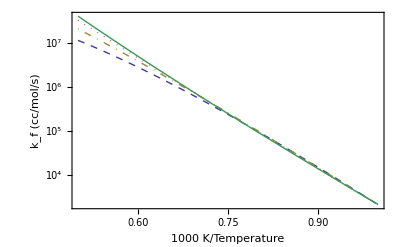

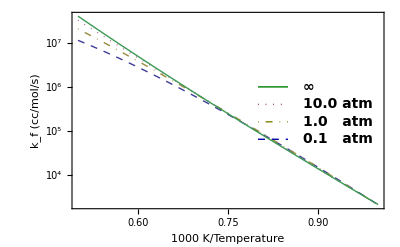

```mathematica
plotframeKeqT={{Style["k_f (cc/mol/s) ",Italic,17],},{Style["1000 K/Temperature",Italic,17],}};
pIverseTFitkforPlottri=LogPlot[pIverseTFitkfortri,{β,0.5,1},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                   PlotStyle-> {Dashed,{Thick,Dotted},{Thick,(*Dashing[{0.01,Small}]*)DotDashed},Thick}]
(*Blue 0.1 atm. Yellow 1.0 atm. Purple 10.0 atm. Green HPL*)
FMTtext={14,Bold};
labelstart=0.80;
labelend=0.85;
textposition=0.875;
toplabel=10^6;
deltalabel=2.5;
plotlable=Graphics[{{Darker[Green,.5],Thick,Line[{{labelstart,Log[toplabel]},{labelend,Log[toplabel]}}]},Text[Style["∞",FMTtext],{textposition,Log[toplabel]},{-1,0}],
                                        {Darker[Red,.5],Dotted,Line[{{labelstart,Log[toplabel/deltalabel]},{labelend,Log[toplabel/deltalabel]}}]},Text[Style["10.0 atm",FMTtext],{textposition,Log[toplabel/deltalabel]},{-1,0}],
                                        {Darker[Yellow,.5],Thick,DotDashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel]}}]},Text[Style["1.0   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel]},{-1,0}],
                                        {Darker[Blue],Dashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel/deltalabel]}}]},Text[Style["0.1   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel/deltalabel]},{-1,0}]}];
Show[pIverseTFitkforPlottri,plotlable]
```

## 2 in 1

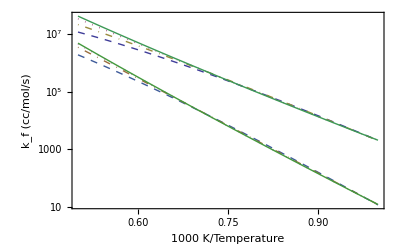

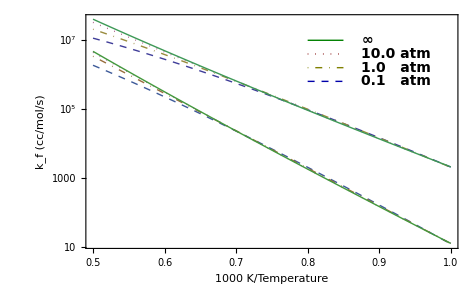

```mathematica
plotframeKeqT={{Style["k_f (cc/mol/s) ",Italic,17],},{Style["1000 K/Temperature",Italic,17],}};
pIverseTFitkforPlot2in1=LogPlot[{pIverseTFitkfortri,pIverseTFitkforsin},{β,0.5,1},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                   PlotStyle-> {Dashed,{Thick,Dotted},{Thick,(*Dashing[{0.01,Small}]*)DotDashed},Thick,Dashed,{Thick,Dotted},{Thick,(*Dashing[{0.01,Small}]*)DotDashed},Thick}]
(*Blue 0.1 atm. Yellow 1.0 atm. Purple 10.0 atm. Green HPL*)
FMTtext={14,Bold};
labelstart=0.80;
labelend=0.85;
textposition=0.875;
toplabel=10^7;
deltalabel=2.5;
plotlable=Graphics[{{Darker[Green,.5],Thick,Line[{{labelstart,Log[toplabel]},{labelend,Log[toplabel]}}]},Text[Style["∞",FMTtext],{textposition,Log[toplabel]},{-1,0}],
                                        {Darker[Red,.5],Dotted,Line[{{labelstart,Log[toplabel/deltalabel]},{labelend,Log[toplabel/deltalabel]}}]},Text[Style["10.0 atm",FMTtext],{textposition,Log[toplabel/deltalabel]},{-1,0}],
                                        {Darker[Yellow,.5],Thick,DotDashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel]}}]},Text[Style["1.0   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel]},{-1,0}],
                                        {Darker[Blue],Dashed,Line[{{labelstart,Log[toplabel/deltalabel/deltalabel/deltalabel]},{labelend,Log[toplabel/deltalabel/deltalabel/deltalabel]}}]},Text[Style["0.1   atm",FMTtext],{textposition,Log[toplabel/deltalabel/deltalabel/deltalabel]},{-1,0}]}];
Show[pIverseTFitkforPlot2in1,plotlable]
```